```mathematica
Do[
v=4;
vv=ToString[v];
ll=ToString[l];
Chi1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-1.txt",{Number,Number}];
Chit1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-1.txt",{Number,Number}];
Chi2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-2.txt",{Number,Number}];
Chit2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-2.txt",{Number,Number}];
Chi3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-3.txt",{Number,Number}];
Chit3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-3.txt",{Number,Number}];
Chi4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-4.txt",{Number,Number}];
Chit4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-4.txt",{Number,Number}];


Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];


Ch4[v][l]=Chi[v][l];
Cht4[v][l]=Chit[v][l];


i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];

,{l,{1,2,4,5,10,20}}]
```

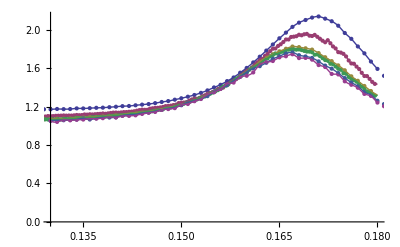

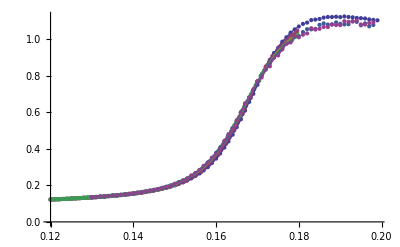

```mathematica
v=4;
pic1=ListPlot[{Ch4[v][1],Ch4[v][2],Ch4[v][4],Ch4[v][5],Ch4[v][10],Ch4[v][20]},PlotRange->{{0.13,0.18},Full}];
pic2=Plot[{i4[v][1][i],i4[v][2][i],i4[v][4][i],i4[v][5][i],i4[v][10][i],i4[v][20][i]},{i,0.13,0.18},PlotRange->Full];
pic3=ListPlot[{Cht4[v][1],Cht4[v][2],Cht4[v][4],Cht4[v][5],Cht4[v][10],Cht4[v][20]},PlotRange->Full];
pic4=Plot[{it4[v][1][i],it4[v][2][i],it4[v][4][i],it4[v][5][i],it4[v][10][i],it4[v][20][i]},{i,0.13,0.18},PlotRange->Full];
Show[{pic1,pic2}]
Show[{pic3,pic4}]
```